```mathematica
SetDirectory[NotebookDirectory[]];
```

Definition of distribution function

nb

```mathematica
nbto[x_,T_]=1/(Exp[x/T]-1);
```

```mathematica
nbd1xto[x_,T_]=D[nbto[x,T],x]/.ⅇ^(x/T)->1+nb[x,T]^(-1)//Simplify;
```

```mathematica
nbd1xrepl={Derivative[1,0][nb][x_,T_]->nbd1xto[x,T]};
```

```mathematica
nbd2xto[x_,T_]=D[nbd1xto[x,T],x]/.nbd1xrepl//FullSimplify;
```

```mathematica
nbd3xto[x_,T_]=D[nbd2xto[x,T],x]/.nbd1xrepl//FullSimplify;
```

```mathematica
nbd4xto[x_,T_]=D[nbd3xto[x,T],x]/.nbd1xrepl//FullSimplify;
```

```mathematica
nbd5xto[x_,T_]=D[nbd4xto[x,T],x]/.nbd1xrepl//FullSimplify;
```

```mathematica
nbd6xto[x_,T_]=D[nbd5xto[x,T],x]/.nbd1xrepl//FullSimplify;
```

```mathematica
nbd0x=nb;
```

```mathematica
nbd1x=nbd1xto[x,T]/.{nb[x,T]->nb};
```

```mathematica
nbd2x=nbd2xto[x,T]/.{nb[x,T]->nb};
```

```mathematica
nbd3x=nbd3xto[x,T]/.{nb[x,T]->nb};
```

```mathematica
nbd4x=nbd4xto[x,T]/.{nb[x,T]->nb};
```

```mathematica
nbd5x=nbd5xto[x,T]/.{nb[x,T]->nb};
```

```mathematica
nbd6x=nbd6xto[x,T]/.{nb[x,T]->nb};
```

```mathematica
(*FortranForm[nbd6x]>>"./nfderi/nbd6x.f90";*)
```

nf

```mathematica
nfto[x_,T_]=1/(Exp[x/T]+1);
```

```mathematica
nfd1xto[x_,T_]=D[nfto[x,T],x]/.ⅇ^(x/T)->-1+nf[x,T]^(-1)//Simplify;
```

```mathematica
nfd1xrepl={Derivative[1,0][nf][x_,T_]->nfd1xto[x,T]};
```

```mathematica
nfd2xto[x_,T_]=D[nfd1xto[x,T],x]/.nfd1xrepl//FullSimplify;
```

```mathematica
nfd3xto[x_,T_]=D[nfd2xto[x,T],x]/.nfd1xrepl//FullSimplify;
```

```mathematica
nfd4xto[x_,T_]=D[nfd3xto[x,T],x]/.nfd1xrepl//FullSimplify;
```

```mathematica
nfd1x=nfd1xto[x,T]/.{nf[x,T]->nf};
```

```mathematica
nfd2x=nfd2xto[x,T]/.{nf[x,T]->nf};
```

```mathematica
nfd3x=nfd3xto[x,T]/.{nf[x,T]->nf};
```

```mathematica
nfd4x=nfd4xto[x,T]/.{nf[x,T]->nf};
```

```mathematica
FortranForm[nfd4x]>>"./nfd4x.f90";
```

nf split

```mathematica
nf0to[x_,T_,l_,lb_]=1/(1+3lb Exp[x/T]+3l Exp[2x/T]+Exp[3x/T]);
```

```mathematica
nf1to[x_,T_,l_,lb_]=2Exp[x/T]nf0[x,T,l,lb];
```

```mathematica
nf2to[x_,T_,l_,lb_]=Exp[2x/T]nf0[x,T,l,lb];
```

```mathematica
Erepl={ⅇ^(x/T)->nf1[x,T,l,lb]/(2nf0[x,T,l,lb]),ⅇ^((2 x)/T)->nf2[x,T,l,lb]/nf0[x,T,l,lb],ⅇ^((3 x)/T)->(1-3/2 lb nf1[x,T,l,lb]-3l nf2[x,T,l,lb]-nf0[x,T,l,lb])/nf0[x,T,l,lb]};
```

```mathematica
nf0repl={(1+ⅇ^((3 x)/T)+3 ⅇ^((2 x)/T) l+3 ⅇ^(x/T) lb)->1/nf0[x,T,l,lb]};
```

```mathematica
nfto[x_,T_,l_,lb_]=nf0to[x,T,l,lb]+lb nf1to[x,T,l,lb]+l nf2to[x,T,l,lb]/.nf0repl/.Erepl;
```

nfd1x

```mathematica
nf0d1xto[x_,T_,l_,lb_]=D[nf0to[x,T,l,lb],x]/.nf0repl/.Erepl//Simplify;
```

```mathematica
nf1d1xto[x_,T_,l_,lb_]=D[nf1to[x,T,l,lb],x]/.Erepl/.Derivative[1,0,0,0][nf0][x_,T_,l_,lb_]->nf0d1xto[x,T,l,lb]//Simplify;
```

```mathematica
nf2d1xto[x_,T_,l_,lb_]=D[nf2to[x,T,l,lb],x]/.Erepl/.Derivative[1,0,0,0][nf0][x_,T_,l_,lb_]->nf0d1xto[x,T,l,lb]//Simplify;
```

```mathematica
nf012d1xrepl={Derivative[1,0,0,0][nf0][x_,T_,l_,lb_]->nf0d1xto[x,T,l,lb],Derivative[1,0,0,0][nf1][x_,T_,l_,lb_]->nf1d1xto[x,T,l,lb],Derivative[1,0,0,0][nf2][x_,T_,l_,lb_]->nf2d1xto[x,T,l,lb]};
```

nfd1l

```mathematica
nf0d1lto[x_,T_,l_,lb_]=D[nf0to[x,T,l,lb],l]/.nf0repl/.Erepl//Simplify;
```

```mathematica
nf1d1lto[x_,T_,l_,lb_]=D[nf1to[x,T,l,lb],l]/.Erepl/. Derivative[0,0,1,0][nf0][x_,T_,l_,lb_]->nf0d1lto[x,T,l,lb]//Simplify;
```

```mathematica
nf2d1lto[x_,T_,l_,lb_]=D[nf2to[x,T,l,lb],l]/.Erepl/. Derivative[0,0,1,0][nf0][x_,T_,l_,lb_]->nf0d1lto[x,T,l,lb]//Simplify;
```

```mathematica
nf012d1lrepl={Derivative[0,0,1,0][nf0][x_,T_,l_,lb_]->nf0d1lto[x,T,l,lb],Derivative[0,0,1,0][nf1][x_,T_,l_,lb_]->nf1d1lto[x,T,l,lb],Derivative[0,0,1,0][nf2][x_,T_,l_,lb_]->nf2d1lto[x,T,l,lb]};
```

nfd1lb

```mathematica
nf0d1lbto[x_,T_,l_,lb_]=D[nf0to[x,T,l,lb],lb]/.nf0repl/.Erepl//Simplify;
```

```mathematica
nf1d1lbto[x_,T_,l_,lb_]=D[nf1to[x,T,l,lb],lb]/.Erepl/. Derivative[0,0,0,1][nf0][x_,T_,l_,lb_]->nf0d1lbto[x,T,l,lb]//Simplify;
```

```mathematica
nf2d1lbto[x_,T_,l_,lb_]=D[nf2to[x,T,l,lb],lb]/.Erepl/. Derivative[0,0,0,1][nf0][x_,T_,l_,lb_]->nf0d1lbto[x,T,l,lb]//Simplify;
```

```mathematica
nf012d1lbrepl={Derivative[0,0,0,1][nf0][x_,T_,l_,lb_]->nf0d1lbto[x,T,l,lb],Derivative[0,0,0,1][nf1][x_,T_,l_,lb_]->nf1d1lbto[x,T,l,lb],Derivative[0,0,0,1][nf2][x_,T_,l_,lb_]->nf2d1lbto[x,T,l,lb]};
```

```mathematica
nf012d1repl={Derivative[1,0,0,0][nf0][x_,T_,l_,lb_]->nf0d1xto[x,T,l,lb],Derivative[1,0,0,0][nf1][x_,T_,l_,lb_]->nf1d1xto[x,T,l,lb],Derivative[1,0,0,0][nf2][x_,T_,l_,lb_]->nf2d1xto[x,T,l,lb],Derivative[0,0,1,0][nf0][x_,T_,l_,lb_]->nf0d1lto[x,T,l,lb],Derivative[0,0,1,0][nf1][x_,T_,l_,lb_]->nf1d1lto[x,T,l,lb],Derivative[0,0,1,0][nf2][x_,T_,l_,lb_]->nf2d1lto[x,T,l,lb],Derivative[0,0,0,1][nf0][x_,T_,l_,lb_]->nf0d1lbto[x,T,l,lb],Derivative[0,0,0,1][nf1][x_,T_,l_,lb_]->nf1d1lbto[x,T,l,lb],Derivative[0,0,0,1][nf2][x_,T_,l_,lb_]->nf2d1lbto[x,T,l,lb]};
```

```mathematica
nfd1lto[x_,T_,l_,lb_]=D[nfto[x,T,l,lb],l]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd1lbto[x_,T_,l_,lb_]=D[nfto[x,T,l,lb],lb]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd1xto[x_,T_,l_,lb_]=D[nfto[x,T,l,lb],x]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd2xto[x_,T_,l_,lb_]=D[nfd1xto[x,T,l,lb],x]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd3xto[x_,T_,l_,lb_]=D[nfd2xto[x,T,l,lb],x]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd4xto[x_,T_,l_,lb_]=D[nfd3xto[x,T,l,lb],x]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd5xto[x_,T_,l_,lb_]=D[nfd4xto[x,T,l,lb],x]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd6xto[x_,T_,l_,lb_]=D[nfd5xto[x,T,l,lb],x]/.nf012d1repl//FullSimplify;
```

```mathematica
nfd0x=nfto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd1x=nfd1xto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd2x=nfd2xto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd3x=nfd3xto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd4x=nfd4xto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd5x=nfd5xto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd6x=nfd6xto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd1l=nfd1lto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
nfd1lb=nfd1lbto[x,T,l,lb]/.{nf0[x,T,l,lb]->nf0,nf1[x,T,l,lb]->nf1,nf2[x,T,l,lb]->nf2};
```

```mathematica
(*FortranForm[nfd6x]>>"./nfderi/nfd6x.f90";*)
```

Mass and its derivatives

```mathematica
mPion2to[rho_]=D[V[rho],rho]/k^2;
```

```mathematica
mSigma2to[rho_]=(D[V[rho],rho]+2rho D[V[rho],{rho,2}])/k^2;
```

```mathematica
mf2to[rho_]=h^2/k^2 rho/Nf;
```

```mathematica
vrepl={Derivative[1][V][rho_]->lam1,Derivative[2][V][rho_]->lam2,Derivative[3][V][rho_]->lam3,Derivative[4][V][rho_]->lam4,Derivative[5][V][rho_]->lam5,Derivative[6][V][rho_]->lam6,Derivative[7][V][rho_]->lam7,Derivative[8][V][rho_]->lam8,Derivative[9][V][rho_]->lam9,Derivative[10][V][rho_]->lam10};
```

```mathematica
mp2E=mPion2to[rho]/.vrepl;
```

```mathematica
ms2E=mSigma2to[rho]/.vrepl;
```

```mathematica
mf2E=mf2to[rho]/.vrepl;
```

Pion

```mathematica
drho1mPion2to[rho_]=D[mPion2to[rho],rho];
```

```mathematica
drho2mPion2to[rho_]=D[drho1mPion2to[rho],rho];
```

```mathematica
drho3mPion2to[rho_]=D[drho2mPion2to[rho],rho];
```

```mathematica
drho4mPion2to[rho_]=D[drho3mPion2to[rho],rho];
```

```mathematica
drho5mPion2to[rho_]=D[drho4mPion2to[rho],rho];
```

```mathematica
drho6mPion2to[rho_]=D[drho5mPion2to[rho],rho];
```

```mathematica
drho7mPion2to[rho_]=D[drho6mPion2to[rho],rho];
```

```mathematica
mp2d1rhoE=drho1mPion2to[rho]/.vrepl;
```

```mathematica
mp2d2rhoE=drho2mPion2to[rho]/.vrepl;
```

```mathematica
mp2d3rhoE=drho3mPion2to[rho]/.vrepl;
```

```mathematica
mp2d4rhoE=drho4mPion2to[rho]/.vrepl;
```

```mathematica
mp2d5rhoE=drho5mPion2to[rho]/.vrepl;
```

Sigma

```mathematica
drho1mSigma2to[rho_]=D[mSigma2to[rho],rho];
```

```mathematica
drho2mSigma2to[rho_]=D[drho1mSigma2to[rho],rho];
```

```mathematica
drho3mSigma2to[rho_]=D[drho2mSigma2to[rho],rho];
```

```mathematica
drho4mSigma2to[rho_]=D[drho3mSigma2to[rho],rho];
```

```mathematica
drho5mSigma2to[rho_]=D[drho4mSigma2to[rho],rho];
```

```mathematica
drho6mSigma2to[rho_]=D[drho5mSigma2to[rho],rho];
```

```mathematica
drho7mSigma2to[rho_]=D[drho6mSigma2to[rho],rho];
```

```mathematica
ms2d1rhoE=drho1mSigma2to[rho]/.vrepl;
```

```mathematica
ms2d2rhoE=drho2mSigma2to[rho]/.vrepl;
```

```mathematica
ms2d3rhoE=drho3mSigma2to[rho]/.vrepl;
```

```mathematica
ms2d4rhoE=drho4mSigma2to[rho]/.vrepl;
```

```mathematica
ms2d5rhoE=drho5mSigma2to[rho]/.vrepl;
```

Fermion

```mathematica
drho1mf2to[rho_]=D[mf2to[rho],rho];
```

```mathematica
drho2mf2to[rho_]=D[drho1mf2to[rho],rho];
```

```mathematica
drho3mf2to[rho_]=D[drho2mf2to[rho],rho];
```

```mathematica
drho4mf2to[rho_]=D[drho3mf2to[rho],rho];
```

```mathematica
drho5mf2to[rho_]=D[drho4mf2to[rho],rho];
```

```mathematica
drho6mf2to[rho_]=D[drho5mf2to[rho],rho];
```

```mathematica
drho7mf2to[rho_]=D[drho6mf2to[rho],rho];
```

```mathematica
mf2d1rhoE=drho1mf2to[rho]/.vrepl;
```

```mathematica
massrepl={mPion2[rho_]->mp2,mSigma2[rho_]->ms2,mf2[rho_]->mf2,Derivative[1][mPion2][rho_]->mp2d1rho,Derivative[2][mPion2][rho_]->mp2d2rho,Derivative[3][mPion2][rho_]->mp2d3rho,Derivative[4][mPion2][rho_]->mp2d4rho,Derivative[5][mPion2][rho_]->mp2d5rho,Derivative[6][mPion2][rho_]->mp2d6rho,Derivative[7][mPion2][rho_]->mp2d7rho,Derivative[1][mSigma2][rho_]->ms2d1rho,Derivative[2][mSigma2][rho_]->ms2d2rho,Derivative[3][mSigma2][rho_]->ms2d3rho,Derivative[4][mSigma2][rho_]->ms2d4rho,Derivative[5][mSigma2][rho_]->ms2d5rho,Derivative[6][mSigma2][rho_]->ms2d6rho,Derivative[7][mSigma2][rho_]->ms2d7rho,Derivative[1][mf2][rho_]->mf2d1rho,Derivative[2][mf2][rho_]->0,Derivative[3][mf2][rho_]->0,Derivative[4][mf2][rho_]->0,Derivative[5][mf2][rho_]->0,Derivative[6][mf2][rho_]->0,Derivative[7][mf2][rho_]->0};
```

```mathematica
(*FortranForm[ee]>>"./ee.f90";*)
```

Replacement

```mathematica
nbnfrepl={nb[(k √(1+mPion2[rho]))/(√zb),T] ->nbPion,nb[(k √(1+mSigma2[rho]))/(√zb),T] ->nbSigma,Derivative[1,0][nb][(k √(1+mPion2[rho]))/(√zb),T]->nbd1xPion,Derivative[1,0][nb][(k √(1+mSigma2[rho]))/(√zb),T]->nbd1xSigma,Derivative[2,0][nb][(k √(1+mPion2[rho]))/(√zb),T]->nbd2xPion,Derivative[2,0][nb][(k √(1+mSigma2[rho]))/(√zb),T]->nbd2xSigma,
Derivative[3,0][nb][(k √(1+mPion2[rho]))/(√zb),T]->nbd3xPion,Derivative[3,0][nb][(k √(1+mSigma2[rho]))/(√zb),T]->nbd3xSigma,
Derivative[4,0][nb][(k √(1+mPion2[rho]))/(√zb),T]->nbd4xPion,Derivative[4,0][nb][(k √(1+mSigma2[rho]))/(√zb),T]->nbd4xSigma,
Derivative[5,0][nb][(k √(1+mPion2[rho]))/(√zb),T]->nbd5xPion,Derivative[5,0][nb][(k √(1+mSigma2[rho]))/(√zb),T]->nbd5xSigma,nf[-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nff,nf[mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfa,Derivative[0,0,1,0][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd1lf,Derivative[0,0,0,1][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd1lba,Derivative[0,0,0,1][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd1lbf,Derivative[0,0,1,0][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd1la,Derivative[1,0,0,0][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd1xf,Derivative[1,0,0,0][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd1xa,Derivative[2,0,0,0][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd2xf,Derivative[2,0,0,0][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd2xa,Derivative[3,0,0,0][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd3xf,Derivative[3,0,0,0][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd3xa,Derivative[4,0,0,0][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd4xf,Derivative[4,0,0,0][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd4xa,Derivative[5,0,0,0][nf][-mu+(k √(1+mf2[rho]))/zf,T,l,lb]->nfd5xf,Derivative[5,0,0,0][nf][mu+(k √(1+mf2[rho]))/zf,T,lb,l]->nfd5xa,nb[k/(√zb),T]->nbGluon,Derivative[1,0][nb][k/(√zb),T]->nbd1xGluon,Derivative[2,0][nb][k/(√zb),T]->nbd2xGluon,Derivative[3,0][nb][k/(√zb),T]->nbd3xGluon,Derivative[4,0][nb][k/(√zb),T]->nbd4xGluon,Derivative[5,0][nb][k/(√zb),T]->nbd5xGluon};
```

```mathematica
BFrepl={b2b2[mb2a_,mb2b_]->-1/(2 √zb)(-(2 (1+2 nb[(k √(1+mb2a))/(√zb),T]))/(√(1+mb2a) (mb2a-mb2b)^3)-(1+2 nb[(k √(1+mb2a))/(√zb),T])/(2 (1+mb2a)^(3/2) (mb2a-mb2b)^2)-(2 (1+2 nb[(k √(1+mb2b))/(√zb),T]))/(√(1+mb2b) (-mb2a+mb2b)^3)-(1+2 nb[(k √(1+mb2b))/(√zb),T])/(2 (1+mb2b)^(3/2) (-mb2a+mb2b)^2)+(k Derivative[1,0][nb][(k √(1+mb2a))/(√zb),T])/((1+mb2a) (mb2a-mb2b)^2 √zb)+(k Derivative[1,0][nb][(k √(1+mb2b))/(√zb),T])/((1+mb2b) (-mb2a+mb2b)^2 √zb)),f2a[mf2_]->1/(4 (1+mf2)^(3/2) zf^2)(zf-zf nf[-mu+(k √(1+mf2))/zf,T,l,lb]-zf nf[mu+(k √(1+mf2))/zf,T,lb,l]+k √(1+mf2) Derivative[1,0,0,0][nf][-mu+(k √(1+mf2))/zf,T,l,lb]+k √(1+mf2) Derivative[1,0,0,0][nf][mu+(k √(1+mf2))/zf,T,lb,l]),f3a[mf2_]->1/(16 (1+mf2)^(5/2) zf^2)(3 (zf-zf nf[-mu+(k √(1+mf2))/zf,T,l,lb]-zf nf[mu+(k √(1+mf2))/zf,T,lb,l]+k √(1+mf2) Derivative[1,0,0,0][nf][-mu+(k √(1+mf2))/zf,T,l,lb]+k √(1+mf2) Derivative[1,0,0,0][nf][mu+(k √(1+mf2))/zf,T,lb,l])-(k^2 (1+mf2) (Derivative[2,0,0,0][nf][-mu+(k √(1+mf2))/zf,T,l,lb]+Derivative[2,0,0,0][nf][mu+(k √(1+mf2))/zf,T,lb,l]))/zf),b2f1a[mb2_,mf2_]->-1/(2 zb zf^2)k^2 (-(k (-mu0+ⅈ p0c-(k √(1+mb2))/(√zb)))/((1+mb2) ((-mu0+ⅈ p0c-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2)^2)+(√zb)/(2 (1+mb2)^(3/2) ((-mu0+ⅈ p0c-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2))-(k^2 zf)/(√(1+mf2) zb (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0c+(k √(1+mf2))/zf)^2)^2)-(k (-mu0+ⅈ p0-(k √(1+mb2))/(√zb)) nb[(k √(1+mb2))/(√zb),T])/((1+mb2) ((-mu0+ⅈ p0-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2)^2)+(√zb nb[(k √(1+mb2))/(√zb),T])/(2 (1+mb2)^(3/2) ((-mu0+ⅈ p0-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2))+(k (-mu0+ⅈ p0+(k √(1+mb2))/(√zb)) nb[(k √(1+mb2))/(√zb),T])/((1+mb2) ((-mu0+ⅈ p0+(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2)^2)+(√zb nb[(k √(1+mb2))/(√zb),T])/(2 (1+mb2)^(3/2) ((-mu0+ⅈ p0+(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2))+1/2 ((k^2 zf nf[-mu+(k √(1+mf2))/zf,T,l,lb])/(√(1+mf2) zb (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0-(k √(1+mf2))/zf)^2)^2)+(k^2 zf nf[mu+(k √(1+mf2))/zf,T,lb,l])/(√(1+mf2) zb (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0-(k √(1+mf2))/zf)^2)^2))+1/2 ((k^2 zf nf[-mu+(k √(1+mf2))/zf,T,l,lb])/(√(1+mf2) zb (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0+(k √(1+mf2))/zf)^2)^2)+(k^2 zf nf[mu+(k √(1+mf2))/zf,T,lb,l])/(√(1+mf2) zb (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0+(k √(1+mf2))/zf)^2)^2))-(k Derivative[1,0][nb][(k √(1+mb2))/(√zb),T])/(2 (1+mb2) ((-mu0+ⅈ p0-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2))-(k Derivative[1,0][nb][(k √(1+mb2))/(√zb),T])/(2 (1+mb2) ((-mu0+ⅈ p0+(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2))),b1f2[mb2_,mf2_]->-1/(2 zb zf^2)k^2 ((k (-mu0+ⅈ p0c+(k √(1+mf2))/zf))/((1+mf2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0c+(k √(1+mf2))/zf)^2)^2)-(k^2 √zb)/(√(1+mb2) ((-mu0+ⅈ p0c-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2)^2 zf^2)+zf/(2 (1+mf2)^(3/2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0c+(k √(1+mf2))/zf)^2))-(k^2 √zb nb[(k √(1+mb2))/(√zb),T])/(√(1+mb2) ((-mu0+ⅈ p0-(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2)^2 zf^2)-(k^2 √zb nb[(k √(1+mb2))/(√zb),T])/(√(1+mb2) ((-mu0+ⅈ p0+(k √(1+mb2))/(√zb))^2-(k^2 (1+mf2))/zf^2)^2 zf^2)+1/2 ((k (mu0+ⅈ p0-(k √(1+mf2))/zf) nf[-mu+(k √(1+mf2))/zf,T,l,lb])/((1+mf2) (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0-(k √(1+mf2))/zf)^2)^2)-(zf nf[-mu+(k √(1+mf2))/zf,T,l,lb])/(2 (1+mf2)^(3/2) (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0-(k √(1+mf2))/zf)^2))+(k (-mu0+ⅈ p0-(k √(1+mf2))/zf) nf[mu+(k √(1+mf2))/zf,T,lb,l])/((1+mf2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0-(k √(1+mf2))/zf)^2)^2)-(zf nf[mu+(k √(1+mf2))/zf,T,lb,l])/(2 (1+mf2)^(3/2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0-(k √(1+mf2))/zf)^2))+(k Derivative[1,0,0,0][nf][-mu+(k √(1+mf2))/zf,T,l,lb])/(2 (1+mf2) (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0-(k √(1+mf2))/zf)^2))+(k Derivative[1,0,0,0][nf][mu+(k √(1+mf2))/zf,T,lb,l])/(2 (1+mf2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0-(k √(1+mf2))/zf)^2)))+1/2 (-(k (-mu0+ⅈ p0+(k √(1+mf2))/zf) nf[-mu+(k √(1+mf2))/zf,T,l,lb])/((1+mf2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0+(k √(1+mf2))/zf)^2)^2)-(zf nf[-mu+(k √(1+mf2))/zf,T,l,lb])/(2 (1+mf2)^(3/2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0+(k √(1+mf2))/zf)^2))-(k (mu0+ⅈ p0+(k √(1+mf2))/zf) nf[mu+(k √(1+mf2))/zf,T,lb,l])/((1+mf2) (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0+(k √(1+mf2))/zf)^2)^2)-(zf nf[mu+(k √(1+mf2))/zf,T,lb,l])/(2 (1+mf2)^(3/2) (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0+(k √(1+mf2))/zf)^2))+(k Derivative[1,0,0,0][nf][-mu+(k √(1+mf2))/zf,T,l,lb])/(2 (1+mf2) (-(k^2 (1+mb2))/zb+(-mu0+ⅈ p0+(k √(1+mf2))/zf)^2))+(k Derivative[1,0,0,0][nf][mu+(k √(1+mf2))/zf,T,lb,l])/(2 (1+mf2) (-(k^2 (1+mb2))/zb+(mu0+ⅈ p0+(k √(1+mf2))/zf)^2))))};
```

Effective potential and its derivatives

```mathematica
l0B4[mb2_]=2/3(1-etaphi/5)1/(√zb)1/(√(1+mb2))(1/2+nb[(k √(1+mb2))/(√zb),T]);
```

```mathematica
l0F4[mf2_,l_,lb_,mu_]=2/3(1-etapsi/4)1/(2zf(1+mf2)^(1/2))(1-nf[(k √(1+mf2))/zf+mu,T,lb,l]-nf[(k √(1+mf2))/zf-mu,T,l,lb]);
```

```mathematica
dtV[rho_,l_,lb_,mu_]=k^4 v3/2((Nf^2-1)l0B4[mPion2[rho]]+l0B4[mSigma2[rho]]-4Nc Nf l0F4[mf2[rho],l,lb,mu]);
```

```mathematica
dtVd1l[rho_,l_,lb_,mu_]=D[dtV[rho,l,lb,mu],l];
```

```mathematica
dtVd1lb[rho_,l_,lb_,mu_]=D[dtV[rho,l,lb,mu],lb];
```

```mathematica
dtVd1rho[rho_,l_,lb_,mu_]=D[dtV[rho,l,lb,mu],rho];
```

```mathematica
dtVd2rho[rho_,l_,lb_,mu_]=D[dtVd1rho[rho,l,lb,mu],rho];
```

```mathematica
dtVd3rho[rho_,l_,lb_,mu_]=D[dtVd2rho[rho,l,lb,mu],rho];
```

```mathematica
dtVd4rho[rho_,l_,lb_,mu_]=D[dtVd3rho[rho,l,lb,mu],rho];
```

```mathematica
dtVd5rho[rho_,l_,lb_,mu_]=D[dtVd4rho[rho,l,lb,mu],rho];
```

```mathematica
dr0dtV=dtV[rho,l,lb,mu]/.nbnfrepl/.massrepl;
```

```mathematica
dr1dtV=dtVd1rho[rho,l,lb,mu]/.nbnfrepl/.massrepl;
```

```mathematica
dr2dtV=dtVd2rho[rho,l,lb,mu]/.nbnfrepl/.massrepl;
```

```mathematica
dr3dtV=dtVd3rho[rho,l,lb,mu]/.nbnfrepl/.massrepl;
```

```mathematica
dr4dtV=dtVd4rho[rho,l,lb,mu]/.nbnfrepl/.massrepl;
```

```mathematica
dr5dtV=dtVd5rho[rho,l,lb,mu]/.nbnfrepl/.massrepl;
```

Two-loop Effective potential and its derivatives

```mathematica
expr=1/180 k^4 v3 (5 Nc (-48 F1 Nf-h^2 v3 ((-1+Nf^2) B2F2c[sqrMPbar[k]]+B2F2c[sqrMSbar[k]]) (-4+etasigmaT[k]))-12 (-1+Nf^2) B1[sqrMPbar[k]] (-5+etasigmaT[k])-12 B1[sqrMSbar[k]] (-5+etasigmaT[k]));
```

```mathematica
dtV[rho_,l_,lb_]=expr/.{F1->F1[mf2[rho],l,lb],B1[sqrMPbar[k]]->B1[mPion2[rho]],B1[sqrMSbar[k]]->B1[mSigma2[rho]],B2F2c[sqrMPbar[k]]->B2F2c[mPion2[rho],mf2[rho],l,lb],B2F2c[sqrMSbar[k]]->B2F2c[mSigma2[rho],mf2[rho],l,lb],etasigmaT[k]->etaphi}//Simplify;
```

```mathematica
dtV[rho,l,lb]/.v3->1/(2 π^2)//FullSimplify;
```

```mathematica
dtVd1l[rho_,l_,lb_]=D[dtV[rho,l,lb],l]//Simplify;
```

```mathematica
dtVd1lb[rho_,l_,lb_]=D[dtV[rho,l,lb],lb]//Simplify;
```

```mathematica
dtVd1rho[rho_,l_,lb_]=D[dtV[rho,l,lb],rho]//Simplify;
```

```mathematica
dtVd2rho[rho_,l_,lb_]=D[dtVd1rho[rho,l,lb],rho]//Simplify;
```

```mathematica
dtVd3rho[rho_,l_,lb_]=D[dtVd2rho[rho,l,lb],rho]//Simplify;
```

```mathematica
dtVd4rho[rho_,l_,lb_]=D[dtVd3rho[rho,l,lb],rho]//Simplify;
```

```mathematica
dtVd5rho[rho_,l_,lb_]=D[dtVd4rho[rho,l,lb],rho]//Simplify;
```

```mathematica
dtVrepl={B1[mp2]->B1P,B1[ms2]->B1S,F1[mf2,l,lb]->F1,B2F2c[mp2,mf2,l,lb]->B2F2cP,B2F2c[ms2,mf2,l,lb]->B2F2cS,Derivative[x_][B1][mp2]:>ToExpression["B1d"<>ToString[x]<>"BP"],Derivative[x_][B1][ms2]:>ToExpression["B1d"<>ToString[x]<>"BS"],Derivative[x_,0,0][F1][mf2,l,lb]:>ToExpression["F1d"<>ToString[x]<>"F"],Derivative[x_,y_,0,0][B2F2c][mp2,mf2,l,lb]:>ToExpression["B2F2cd"<>ToString[x]<>"Bd"<>ToString[y]<>"FP"],Derivative[x_,y_,0,0][B2F2c][ms2,mf2,l,lb]:>ToExpression["B2F2cd"<>ToString[x]<>"Bd"<>ToString[y]<>"FS"],Derivative[0,x_,0][F1][mf2,l,lb]:>ToExpression["F1d"<>ToString[x]<>"l"],Derivative[0,0,x_,0][B2F2c][mp2,mf2,l,lb]:>ToExpression["B2F2cd"<>ToString[x]<>"lP"],Derivative[0,0,x_,0][B2F2c][ms2,mf2,l,lb]:>ToExpression["B2F2cd"<>ToString[x]<>"lS"],Derivative[0,0,x_][F1][mf2,l,lb]:>ToExpression["F1d"<>ToString[x]<>"lb"],Derivative[0,0,0,x_][B2F2c][mp2,mf2,l,lb]:>ToExpression["B2F2cd"<>ToString[x]<>"lbP"],Derivative[0,0,0,x_][B2F2c][ms2,mf2,l,lb]:>ToExpression["B2F2cd"<>ToString[x]<>"lbS"]};
```

```mathematica
dr0dtV=dtV[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dr1dtV=dtVd1rho[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dr2dtV=dtVd2rho[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dr3dtV=dtVd3rho[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dr4dtV=dtVd4rho[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dr5dtV=dtVd5rho[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dtVd1lE=dtVd1l[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dtVd1lbE=dtVd1lb[rho,l,lb]/.massrepl/.dtVrepl//Simplify;
```

```mathematica
dtVd1lb[rho,l,lb]/.massrepl
```

1/36 k^4 Nc v3 (-48 Nf F1^(0,0,1)[mf2,l,lb]-(-4+etaphi) h^2 v3 ((-1+Nf^2) B2F2c^(0,0,0,1)[mp2,mf2,l,lb]+B2F2c^(0,0,0,1)[ms2,mf2,l,lb]))

Threshold functions

BB

```mathematica
b1b1[mb2a_,mb2b_,zb_,T_,k_]=-1/2 1/(√zb)((1+2nb[(k √(1+mb2a))/(√zb),T])1/(√(1+mb2a)(mb2a-mb2b))+(1+2nb[(k √(1+mb2b))/(√zb),T])1/(√(1+mb2b)(mb2b-mb2a)));
```

```mathematica
b2b1[mb2a_,mb2b_,zb_,T_,k_]=-D[b1b1[mb2a,mb2b,zb,T,k],mb2a];
```

```mathematica
b2b2[mb2a_,mb2b_,zb_,T_,k_]=-D[b2b1[mb2a,mb2b,zb,T,k],mb2b];
```

BBFp

```mathematica
b1b1f1f1pExpr=1/2 k^7/(zb^2 zf^4)(nf[mu+(k √(1+mf2b))/zf,T] 1/(k/zf √(1+mf2b))1/((mu-I p0+k/zf √(1+mf2b))^2-(1+mb2a)k^2/zb)1/((mu-I p0+k/zf √(1+mf2b))^2-(1+mb2b)k^2/zb)1/((2mu-2I p0+k/zf √(1+mf2b))^2-(1+mf2a)k^2/zf^2)+(nf[-mu+(k √(1+mf2b))/zf,T]-1)1/(k/zf √(1+mf2b))1/((mu-I p0-k/zf √(1+mf2b))^2-(1+mb2a)k^2/zb)1/((mu-I p0-k/zf √(1+mf2b))^2-(1+mb2b)k^2/zb)1/((2mu-2I p0-k/zf √(1+mf2b))^2-(1+mf2a)k^2/zf^2)+nf[-mu+(k √(1+mf2a))/zf,T] 1/(k/zf √(1+mf2a))1/((I p0-mu+k/zf √(1+mf2a))^2-(1+mb2a)k^2/zb)1/((I p0-mu+k/zf √(1+mf2a))^2-(1+mb2b)k^2/zb)1/((2I p0-2mu+k/zf √(1+mf2a))^2-(1+mf2b)k^2/zf^2)+(nf[mu+(k √(1+mf2a))/zf,T]-1)1/(k/zf √(1+mf2a))1/((I p0-mu-k/zf √(1+mf2a))^2-(1+mb2a)k^2/zb)1/((I p0-mu-k/zf √(1+mf2a))^2-(1+mb2b)k^2/zb)1/((2I p0-2mu-k/zf √(1+mf2a))^2-(1+mf2b)k^2/zf^2)-nb[(k √(1+mb2a))/(√zb),T] 1/(k/(√zb)√(1+mb2a))1/(k^2/zb(mb2a-mb2b))1/((mu-I p0+k/(√zb)√(1+mb2a))^2-(1+mf2a)k^2/zf^2)1/((-mu+I p0+k/(√zb)√(1+mb2a))^2-(1+mf2b)k^2/zf^2)-(nb[(k √(1+mb2a))/(√zb),T]+1)1/(k/(√zb)√(1+mb2a))1/(k^2/zb(mb2a-mb2b))1/((mu-I p0-k/(√zb)√(1+mb2a))^2-(1+mf2a)k^2/zf^2)1/((-mu+I p0-k/(√zb)√(1+mb2a))^2-(1+mf2b)k^2/zf^2)-nb[(k √(1+mb2b))/(√zb),T] 1/(k/(√zb)√(1+mb2b))1/(k^2/zb(mb2b-mb2a))1/((mu-I p0+k/(√zb)√(1+mb2b))^2-(1+mf2a)k^2/zf^2)1/((-mu+I p0+k/(√zb)√(1+mb2b))^2-(1+mf2b)k^2/zf^2)-(nb[(k √(1+mb2b))/(√zb),T]+1)1/(k/(√zb)√(1+mb2b))1/(k^2/zb(mb2b-mb2a))1/((mu-I p0-k/(√zb)√(1+mb2b))^2-(1+mf2a)k^2/zf^2)1/((-mu+I p0-k/(√zb)√(1+mb2b))^2-(1+mf2b)k^2/zf^2));
```

```mathematica
b1b1f1f1pExpr2=b1b1f1f1pExpr//Expand;
```

```mathematica
b1b1f1f1pExpr3=(b1b1f1f1pExpr2-(b1b1f1f1pExpr2/.{nb[__]->0,nf[__]->0}))+(b1b1f1f1pExpr2/.{nb[__]->0,nf[__]->0}/.{p0->p0c});
```

```mathematica
b1b1f1f1pExpr4=b1b1f1f1pExpr3/.{mu->mu0};
```

```mathematica
b1b1f1f1pExpr5=b1b1f1f1pExpr4/.{nf[-mu0+x_,y_]->nf[-mu+x,y,l,lb],nf[mu0+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
b1b1f1f1p[mb2a_,mb2b_,mf2a_,mf2b_,zb_,zf_,T_,mu_,k_,p0_]=b1b1f1f1pExpr5;
```

```mathematica
b1b1f2p[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=b1b1f1f1p[mb2a,mb2b,mf2a,mf2b,zb,zf,T,mu,k,p0]/.{mf2a->mf2,mf2b->mf2};
```

```mathematica
b1b1f3p[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1b1f1f1p[mb2a,mb2b,mf2a,mf2b,zb,zf,T,mu,k,p0],mf2b]/.{mf2a->mf2,mf2b->mf2};
```

```mathematica
b2b1f2p[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1b1f1f1p[mb2a,mb2b,mf2a,mf2b,zb,zf,T,mu,k,p0],mb2a]/.{mf2a->mf2,mf2b->mf2};
```

```mathematica
B1B1F3pPSExpr=b1b1f3p[mPion2[rho],mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2B1F2pPSExpr=b2b1f2p[mPion2[rho],mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2B1F2pSPExpr=b2b1f2p[mSigma2[rho],mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

BBFa

```mathematica
b1b1f1aExpr=1/2 k^5/(zb^2 zf^2)(nb[(k √(1+mb2a))/(√zb),T] 1/(k/(√zb)√(1+mb2a))1/(k^2/zb(mb2a-mb2b))1/((mu-I p0+k/(√zb)√(1+mb2a))^2-(1+mf2)k^2/zf^2)+(nb[(k √(1+mb2a))/(√zb),T]+1)1/(k/(√zb)√(1+mb2a))1/(k^2/zb(mb2a-mb2b))1/((mu-I p0-k/(√zb)√(1+mb2a))^2-(1+mf2)k^2/zf^2)+nb[(k √(1+mb2b))/(√zb),T] 1/(k/(√zb)√(1+mb2b))1/(k^2/zb(mb2b-mb2a))1/((mu-I p0+k/(√zb)√(1+mb2b))^2-(1+mf2)k^2/zf^2)+(nb[(k √(1+mb2b))/(√zb),T]+1)1/(k/(√zb)√(1+mb2b))1/(k^2/zb(mb2b-mb2a))1/((mu-I p0-k/(√zb)√(1+mb2b))^2-(1+mf2)k^2/zf^2)-nf[-mu+(k √(1+mf2))/zf,T] 1/(k/zf √(1+mf2))1/((I p0-mu+k/zf √(1+mf2))^2-(1+mb2a)k^2/zb)1/((I p0-mu+k/zf √(1+mf2))^2-(1+mb2b)k^2/zb)-(nf[mu+(k √(1+mf2))/zf,T]-1)1/(k/zf √(1+mf2))1/((I p0-mu-k/zf √(1+mf2))^2-(1+mb2a)k^2/zb)1/((I p0-mu-k/zf √(1+mf2))^2-(1+mb2b)k^2/zb));
```

```mathematica
b1b1f1aExpr2=b1b1f1aExpr//Expand;
```

```mathematica
b1b1f1aExpr3=(b1b1f1aExpr2-(b1b1f1aExpr2/.{nb[__]->0,nf[__]->0}))+(b1b1f1aExpr2/.{nb[__]->0,nf[__]->0}/.{p0->p0c});
```

```mathematica
b1b1f1aExpr4=b1b1f1aExpr3/.{mu->mu0};
```

```mathematica
b1b1f1aExpr5=b1b1f1aExpr4/.{nf[-mu0+x_,y_]->nf[-mu+x,y,l,lb],nf[mu0+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
b1b1f1a[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=b1b1f1aExpr5;
```

```mathematica
b2b1f1a[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1b1f1a[mb2a,mb2b,mf2,zb,zf,T,mu,k,p0],mb2a];
```

```mathematica
b2b1f2a[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b2b1f1a[mb2a,mb2b,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b1b1f2a[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1b1f1a[mb2a,mb2b,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b1b1f3a[mb2a_,mb2b_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-(1/2)D[b1b1f2a[mb2a,mb2b,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
B2B1F1aPSExpr=b2b1f1a[mPion2[rho],mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2B1F1aSPExpr=b2b1f1a[mSigma2[rho],mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B1B1F2aPSExpr=b1b1f2a[mPion2[rho],mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B1B1F3aPSExpr=b1b1f3a[mPion2[rho],mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2B1F2aPSExpr=b2b1f2a[mPion2[rho],mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2B1F2aSPExpr=b2b1f2a[mSigma2[rho],mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

BF

```mathematica
b1f1Expr=(1/2)(k^2/zb/zf^2)(-nb[(k √(1+mb2))/zb^(1/2),T](zb^(1/2)/√(1+mb2))(1/(((I p0-mu)+k/zb^(1/2)√(1+mb2))^2-(1+mf2)(k/zf)^2))-(nb[(k √(1+mb2))/zb^(1/2),T]+1)(zb^(1/2)/√(1+mb2))(1/(((I p0-mu)-k/zb^(1/2)√(1+mb2))^2-(1+mf2)(k/zf)^2))+nf[mu+(k √(1+mf2))/zf,T](zf/√(1+mf2))(1/(((I p0-mu)-k/zf √(1+mf2))^2-(1+mb2)(k^2/zb)))+(nf[-mu+(k √(1+mf2))/zf,T]-1)(zf/√(1+mf2))(1/(((I p0-mu)+k/zf √(1+mf2))^2-(1+mb2)(k^2/zb))));
```

```mathematica
b1f1Expr2=b1f1Expr//Expand;
```

```mathematica
b1f1Expr3=(b1f1Expr2-(b1f1Expr2/.{nb[__]->0,nf[__]->0}))+(b1f1Expr2/.{nb[__]->0,nf[__]->0}/.{p0->p0c});
```

```mathematica
b1f1Expr4=b1f1Expr3/.{mu->mu0};
```

```mathematica
b1f1Expr5=b1f1Expr4/.{nf[-mu0+x_,y_]->nf[-mu+x,y,l,lb],nf[mu0+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
b1f1[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=b1f1Expr5;
```

```mathematica
b1f2[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1f1[mb2,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b1f3[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-(1/2)D[b1f2[mb2,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b2f1a[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1f1[mb2,mf2,zb,zf,T,mu,k,p0],mb2];
```

```mathematica
b2f2a[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b2f1a[mb2,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b3f1a[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-(1/2)D[b2f1a[mb2,mf2,zb,zf,T,mu,k,p0],mb2];
```

```mathematica
b3f2a[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b3f1a[mb2,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b2f3a[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-(1/2)D[b2f2a[mb2,mf2,zb,zf,T,mu,k,p0],mf2];
```

```mathematica
b2f1aPExpr=b2f1a[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b2f1aSExpr=b2f1a[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f2PExpr=b1f2[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f2SExpr=b1f2[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b2f2aPExpr=b2f2a[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b2f2aSExpr=b2f2a[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f3PExpr=b1f3[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f3SExpr=b1f3[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b3f1aPExpr=b3f1a[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b3f1aSExpr=b3f1a[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b2f1aAExpr=b2f1a[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f2AExpr=b1f2[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b2f2aAExpr=b2f2a[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f3AExpr=b1f3[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b3f1aAExpr=b3f1a[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b2f3aAExpr=b2f3a[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b3f2aAExpr=b3f2a[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2F3aPExpr=b2f3a[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2F3aSExpr=b2f3a[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B3F2aPExpr=b3f2a[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B3F2aSExpr=b3f2a[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
b1f1AExpr=b1f1[0,mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

Fa

```mathematica
f1aExpr=1/(2zf(1+mf2)^(1/2))(1-nf[(k √(1+mf2))/zf+mu,T,lb,l]-nf[(k √(1+mf2))/zf-mu,T,l,lb]);
```

```mathematica
f1a[mf2_,zf_,T_,mu_,k_]=f1aExpr
```

```mathematica
f2a[mf2_,zf_,T_,mu_,k_]=-D[f1a[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f3a[mf2_,zf_,T_,mu_,k_]=-(1/2)D[f2a[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f4a[mf2_,zf_,T_,mu_,k_]=-(1/3)D[f3a[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f2aExpr=f2a[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
f3aExpr=f3a[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
f4aExpr=f4a[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

FaT

```mathematica
(*finite T part of Fa*)
```

```mathematica
f1aTExpr=1/(2zf(1+mf2)^(1/2))(-nf[(k √(1+mf2))/zf+mu,T,lb,l]-nf[(k √(1+mf2))/zf-mu,T,l,lb]);
```

```mathematica
f1aT[mf2_,zf_,T_,mu_,k_]=f1aTExpr;
```

```mathematica
f2aT[mf2_,zf_,T_,mu_,k_]=-D[f1aT[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f3aT[mf2_,zf_,T_,mu_,k_]=-(1/2)D[f2aT[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f4aT[mf2_,zf_,T_,mu_,k_]=-(1/3)D[f3aT[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f2aTExpr=f2aT[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
f3aTExpr=f3aT[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
f4aTExpr=f4aT[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

Fa(modified)

```mathematica
f1aExpr=1/(2zf(1+mf2)^(1/2))(1-nf[(k √(1+mf2))/zf+mu,T,lb,l]-nf[(k √(1+mf2))/zf-mu,T,l,lb])-T/k 1/(((π T)/k)^2+1+mf2);
```

```mathematica
f1a[mf2_,zf_,T_,mu_,k_]=f1aExpr;
```

```mathematica
f2a[mf2_,zf_,T_,mu_,k_]=-D[f1a[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f3a[mf2_,zf_,T_,mu_,k_]=-(1/2)D[f2a[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f4a[mf2_,zf_,T_,mu_,k_]=-(1/3)D[f3a[mf2,zf,T,mu,k],mf2]//Simplify;
```

```mathematica
f2aExpr=f2a[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
f3aExpr=f3a[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
f4aExpr=f4a[mf2[rho],zf,T,mu,k]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

BFp

```mathematica
b1f1f1pExpr=-1/2 k^5/(zb zf^4)(nf[mu+(k √(1+mf2b))/zf,T] 1/(k/zf √(1+mf2b))1/((mu-I p0+k/zf √(1+mf2b))^2-(1+mb2)k^2/zb)1/((2mu-2I p0+k/zf √(1+mf2b))^2-(1+mf2a)k^2/zf^2)+(nf[-mu+(k √(1+mf2b))/zf,T]-1)1/(k/zf √(1+mf2b))1/((mu-I p0-k/zf √(1+mf2b))^2-(1+mb2)k^2/zb)1/((2mu-2I p0-k/zf √(1+mf2b))^2-(1+mf2a)k^2/zf^2)+nf[-mu+(k √(1+mf2a))/zf,T] 1/(k/zf √(1+mf2a))1/((I p0-mu+k/zf √(1+mf2a))^2-(1+mb2)k^2/zb)1/((2I p0-2mu+k/zf √(1+mf2a))^2-(1+mf2b)k^2/zf^2)+(nf[mu+(k √(1+mf2a))/zf,T]-1)1/(k/zf √(1+mf2a))1/((I p0-mu-k/zf √(1+mf2a))^2-(1+mb2)k^2/zb)1/((2I p0-2mu-k/zf √(1+mf2a))^2-(1+mf2b)k^2/zf^2)-nb[(k √(1+mb2))/(√zb),T] 1/(k/(√zb)√(1+mb2))1/((mu-I p0+k/(√zb)√(1+mb2))^2-(1+mf2a)k^2/zf^2)1/((-mu+I p0+k/(√zb)√(1+mb2))^2-(1+mf2b)k^2/zf^2)-(nb[(k √(1+mb2))/(√zb),T]+1)1/(k/(√zb)√(1+mb2))1/((mu-I p0-k/(√zb)√(1+mb2))^2-(1+mf2a)k^2/zf^2)1/((-mu+I p0-k/(√zb)√(1+mb2))^2-(1+mf2b)k^2/zf^2));
```

```mathematica
b1f1f1pExpr2=b1f1f1pExpr//Expand;
```

```mathematica
b1f1f1pExpr3=(b1f1f1pExpr2-(b1f1f1pExpr2/.{nb[__]->0,nf[__]->0}))+(b1f1f1pExpr2/.{nb[__]->0,nf[__]->0}/.{p0->p0c});
```

```mathematica
b1f1f1pExpr4=b1f1f1pExpr3/.{mu->mu0};
```

```mathematica
b1f1f1pExpr5=b1f1f1pExpr4/.{nf[-mu0+x_,y_]->nf[-mu+x,y,l,lb],nf[mu0+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
b1f1f1p[mb2_,mf2a_,mf2b_,zb_,zf_,T_,mu_,k_,p0_]=b1f1f1pExpr5;
```

```mathematica
b2f1f1p[mb2_,mf2a_,mf2b_,zb_,zf_,T_,mu_,k_,p0_]=-D[b1f1f1p[mb2,mf2a,mf2b,zb,zf,T,mu,k,p0],mb2];
```

```mathematica
b2f2p[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=b2f1f1p[mb2,mf2a,mf2b,zb,zf,T,mu,k,p0]/.{mf2a->mf2,mf2b->mf2};
```

```mathematica
b2f3p[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-D[b2f1f1p[mb2,mf2a,mf2b,zb,zf,T,mu,k,p0],mf2b]/.{mf2a->mf2,mf2b->mf2};
```

```mathematica
b3f2p[mb2_,mf2_,zb_,zf_,T_,mu_,k_,p0_]=-(1/2)D[b2f1f1p[mb2,mf2a,mf2b,zb,zf,T,mu,k,p0],mb2]/.{mf2a->mf2,mf2b->mf2};
```

```mathematica
B2F3pPExpr=b2f3p[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B2F3pSExpr=b2f3p[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B3F2pPExpr=b3f2p[mPion2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

```mathematica
B3F2pSExpr=b3f2p[mSigma2[rho],mf2[rho],zb,zf,T,mu,k,p0]/.nbnfrepl/.massrepl/.{zb-> 1,zf-> 1};
```

Fdnf1

```mathematica
nfFdnfRepl={nf[mu+k √(mf2+q2a),T,lb,l]->nfa,nf[mu+k √(mf2+q2b),T,lb,l]->nfaqmp,Derivative[1,0,0,0][nf][mu+k √(mf2+q2a),T,lb,l]->nfd1xa,nf[-mu+k √(mf2+q2a),T,l,lb]->nff,nf[-mu+k √(mf2+q2b),T,l,lb]->nffqmp,Derivative[1,0,0,0][nf][-mu+k √(mf2+q2a),T,l,lb]->nfd1xf};
```

```mathematica
EqRepl={ √(mf2+q2a)->Eq/k,√(mf2+q2b)->Eqmp/k,1/(√(mf2+q2a))->(Eq/k)^-1,1/(√(mf2+q2b))->(Eqmp/k)^-1,1/(mf2+q2a)^(3/2)->(Eq/k)^-3};
```

```mathematica
FdnfRepl={Fdnf1[__]->Fdnf1,Fdnf2[__]->Fdnf2,Derivative[1,0][Fdnf1][__]->Fdnf1d1,Derivative[1,0][Fdnf2][__]->Fdnf2d1};
```

```mathematica
Fdnf1Expr=(-nf[mu+k √(q2a+ mf2a),T]+nf[mu+k √(q2b+ mf2b),T])1/(I p0-k √(q2a+ mf2a)+k √(q2b+ mf2b));
```

```mathematica
(*k √(q2a+ mf2a)=Eq,k √(q2b+ mf2b)=E(q-p)*)
```

```mathematica
Fdnf1Expr2=Fdnf1Expr/.{nf[-mu+x_,y_]->nf[-mu+x,y,l,lb],nf[mu+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
Fdnf1[mf2a_,mf2b_]=Fdnf1Expr2;
```

```mathematica
Fdnf1d1[mf2a_,mf2b_]=D[Fdnf1[mf2a,mf2b],mf2a];
```

```mathematica
Fdnf1ToExpr=Fdnf1[mf2,mf2]/.nfFdnfRepl/.EqRepl/.{p0->0};
```

```mathematica
(*when Eq->Eqmp Fdnf1 is approached to its limit value Fdnf1Lim*)
```

```mathematica
Fdnf1LimToExpr=nfd1xa;
```

```mathematica
Fdnf1d1ToExpr=Fdnf1d1[mf2,mf2]/.nfFdnfRepl/.EqRepl/.{p0->0};
```

```mathematica
Fdnf1d1LimToExpr=k^2/(4Eq)nfd2xa;
```

Fdnf2

```mathematica
Fdnf2Expr=(nf[-mu+k √(q2a+ mf2a),T]-nf[-mu+k √(q2b+ mf2b),T])1/(I p0+k √(q2a+ mf2a)-k √(q2b+ mf2b));
```

```mathematica
Fdnf2Expr2=Fdnf2Expr/.{nf[-mu+x_,y_]->nf[-mu+x,y,l,lb],nf[mu+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
Fdnf2[mf2a_,mf2b_]=Fdnf2Expr2;
```

```mathematica
Fdnf2d1[mf2a_,mf2b_]=D[Fdnf2[mf2a,mf2b],mf2a];
```

```mathematica
Fdnf2ToExpr=Fdnf2[mf2,mf2]/.nfFdnfRepl/.EqRepl/.{p0->0};
```

```mathematica
(*when Eq->Eqmp Fdnf2 is approached to its limit value Fdnf2Lim*)
```

```mathematica
Fdnf2LimToExpr=nfd1xf;
```

```mathematica
Fdnf2d1ToExpr=Fdnf2d1[mf2,mf2]/.nfFdnfRepl/.EqRepl/.{p0->0}
```

(k^2 nfd1xf)/(2 Eq (Eq-Eqmp))-(k^2 (nff-nffqmp))/(2 Eq (Eq-Eqmp)^2)

```mathematica
Fdnf2d1LimToExpr=k^2/(4Eq)nfd2xf;
```

FF

```mathematica
Clear[Fdnf1];
Clear[Fdnf2];
```

```mathematica
F1F1Expr=k^3/(4k √(q2a+ mf2a)k √(q2b+ mf2b))((-1+nf[-mu+k √(q2b+ mf2b),T]+nf[mu+k √(q2a+ mf2a),T])1/(I p0-k √(q2a+ mf2a)-k √(q2b+ mf2b))+Fdnf1[mf2a,mf2b]+Fdnf2[mf2a,mf2b]+(1-nf[-mu+k √(q2a+ mf2a),T]-nf[mu+k √(q2b+ mf2b),T])1/(I p0+k √(q2a+ mf2a)+k √(q2b+ mf2b)));
```

```mathematica
F1F1Expr2=F1F1Expr/.{nf[-mu+x_,y_]->nf[-mu+x,y,l,lb],nf[mu+x_,y_]->nf[mu+x,y,lb,l]};
```

```mathematica
F1F1[mf2a_,mf2b_]=F1F1Expr2;
```

```mathematica
F2F1[mf2a_,mf2b_]=-D[F1F1[mf2a,mf2b],mf2a];
```

```mathematica
F1F1ToExpr=F1F1[mf2,mf2]/.nfFdnfRepl/.EqRepl/.FdnfRepl/.{p0->0};
```

```mathematica
F2F1ToExpr=F2F1[mf2,mf2]/.nfFdnfRepl/.EqRepl/.FdnfRepl/.{p0->0};
```

BBBA

```mathematica
B1B1B1AExpr=k^5/(2Eqa(Eqa^2-Eqb^2)(Eqa^2-Eqc^2))(0+2nb[Eqa,T])+k^5/(2Eqb(Eqb^2-Eqa^2)(Eqb^2-Eqc^2))(0+2nb[Eqb,T])+k^5/(2Eqc(Eqc^2-Eqa^2)(Eqc^2-Eqb^2))(0+2nb[Eqc,T])/.{ Eqa->k √(q2a+mb2a),Eqb->k √(q2b+mb2b),Eqc->k √(q2c+mb2c)(*q2a=1,q2b=q^2/k^2,q2c=(q-p)^2/k^2*)}//Simplify;
```

```mathematica
B1B1B1A[mb2a_,mb2b_,mb2c_]=B1B1B1AExpr;
```

```mathematica
B2B1B1A[mb2a_,mb2b_,mb2c_]=-D[B1B1B1A[mb2a,mb2b,mb2c],mb2a];
```

```mathematica
B3B1B1A[mb2a_,mb2b_,mb2c_]=-1/2 D[B2B1B1A[mb2a,mb2b,mb2c],mb2a];
```

```mathematica
B2B1B2A[mb2a_,mb2b_,mb2c_]=-D[B2B1B1A[mb2a,mb2b,mb2c],mb2c];
```

```mathematica
B3B1B1AToExpr=B3B1B1A[0,0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B2B1B2AToExpr=B2B1B2A[0,0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B2B1B1AToExpr=B2B1B1A[0,0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

BBA

```mathematica
B1B1AExpr=-k^3/(2Eqa(Eqa^2-Eqb^2))(0+2nb[Eqa,T])-k^3/(2Eqb(Eqb^2-Eqa^2))(0+2nb[Eqb,T])/.{ Eqa->k √(q2a+mb2a),Eqb->k √(q2b+mb2b),Eqc->k √(q2c+mb2c)(*q2a=1,q2b=q^2/k^2,q2c=(q-p)^2/k^2*)}//Simplify;
```

```mathematica
B1B1A[mb2a_,mb2b_]=B1B1AExpr;
```

```mathematica
B2B1A[mb2a_,mb2b_]=-D[B1B1A[mb2a,mb2b],mb2a];
```

```mathematica
B2B2A[mb2a_,mb2b_]=-D[B2B1A[mb2a,mb2b],mb2b];
```

```mathematica
B3B1A[mb2a_,mb2b_]=-1/2 D[B2B1A[mb2a,mb2b],mb2a];
```

```mathematica
B4B1A[mb2a_,mb2b_]=-1/3 D[B3B1A[mb2a,mb2b],mb2a];
```

```mathematica
B3B2A[mb2a_,mb2b_]=-D[B3B1A[mb2a,mb2b],mb2b];
```

```mathematica
B4B1AToExpr=B4B1A[0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[3,0][nb][k √q2a,T]->nbd3xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B3B2AToExpr=B3B2A[0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[3,0][nb][k √q2a,T]->nbd3xGluon,Derivative[1,0][nb][k √q2b,T]->nbd1xqGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B3B1AToExpr=B3B1A[0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[3,0][nb][k √q2a,T]->nbd3xGluon,Derivative[1,0][nb][k √q2b,T]->nbd1xqGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B2B0B1AToExpr=B2B1A[0,0]/.{q2b->q2c}/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B2B1AToExpr=B2B1A[0,0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[3,0][nb][k √q2a,T]->nbd3xGluon,Derivative[1,0][nb][k √q2b,T]->nbd1xqGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B2B0B2AToExpr=B2B2A[0,0]/.{q2b->q2c}/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B3B0B1AToExpr=B3B1A[0,0]/.{q2b->q2c}/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

BA

```mathematica
B1AExpr=k/(2Eqa)(0+2nb[Eqa,T])/.{ Eqa->k √(q2a+mb2a),Eqb->k √(q2b+mb2b),Eqc->k √(q2c+mb2c)(*q2a=1,q2b=q^2/k^2,q2c=(q-p)^2/k^2*)}//Simplify;
```

```mathematica
B1A[mb2a_]=B1AExpr;
```

```mathematica
B2A[mb2a_]=-D[B1A[mb2a],mb2a];
```

```mathematica
B3A[mb2a_]=-1/2 D[B2A[mb2a],mb2a];
```

```mathematica
B3AToExpr=B3A[0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
B2AToExpr=B2A[0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

FFGh (ghost)

```mathematica
F1F1GhExpr=k^3/(2Eqa(Eqa^2-Eqb^2))(0+2nf[Eqa,T])+k^3/(2Eqb(Eqb^2-Eqa^2))(0+2nf[Eqb,T])/.{ Eqa->k √(q2a+mb2a),Eqb->k √(q2b+mb2b),Eqc->k √(q2c+mb2c)(*q2a=1,q2b=q^2/k^2,q2c=(q-p)^2/k^2*)}//Simplify;
```

```mathematica
F1F1Gh[mb2a_,mb2b_]=F1F1GhExpr;
```

```mathematica
F2F1Gh[mb2a_,mb2b_]=-D[F1F1Gh[mb2a,mb2b],mb2a];
```

```mathematica
F2F0F1GhToExpr=F2F1Gh[0,0]/.{q2b->q2c}/.{nf[k √q2a,T]->nfGhost,Derivative[1,0][nf][k √q2a,T]->nfd1xGhost,nf[k √q2c,T]->nfqmpGhost}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

FGh (ghost)

```mathematica
F1GhExpr=k/(2Eqa)(0-2nf[Eqa,T])/.{ Eqa->k √(q2a+mb2a),Eqb->k √(q2b+mb2b),Eqc->k √(q2c+mb2c)(*q2a=1,q2b=q^2/k^2,q2c=(q-p)^2/k^2*)}//Simplify;
```

```mathematica
F1Gh[mb2a_]=F1GhExpr;
```

```mathematica
F2Gh[mb2a_]=-D[F1Gh[mb2a],mb2a];
```

```mathematica
F3Gh[mb2a_]=-1/2 D[F2Gh[mb2a],mb2a];
```

```mathematica
B3AToExpr=B3A[0]/. {nb[k √q2a,T]->nbGluon,nb[k √q2b,T]->nbqGluon,nb[k √q2c,T]->nbqmpGluon,Derivative[1,0][nb][k √q2a,T]->nbd1xGluon,Derivative[2,0][nb][k √q2a,T]->nbd2xGluon,Derivative[1,0][nb][k √q2c,T]->nbd1xqmpGluon}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
F3GhToExpr=F3Gh[0]/.{nf[k √q2a,T]->nfGhost,Derivative[1,0][nf][k √q2a,T]->nfd1xGhost,Derivative[2,0][nf][k √q2a,T]->nfd2xGhost}/.{q2a->1,q2b->q2t,q2c->qmp2t};
```

```mathematica
FortranForm[F3GhToExpr]>>"./F3Gh.f90";
```

Wave function renormalization(old)

```mathematica
M12gTo=(1-etaA/(4+1)) (1+mf2[rho])^-1 ;
```

```mathematica
M11To=2/(4-1) (1+mf2[rho])^-1  (-(1/2) (1-2/4 etapsi)+(1-etaA/(4+1))+(1-2/4 etapsi) (1+mf2[rho])^-1);
```

```mathematica
etaphiEq=v3/3(4/k^2 rho (Derivative[2][V][rho])^2 b2b2[mPion2[rho],mSigma2[rho]]+Nc h^2((2etapsi-3)f2a[mf2[rho]]-4(etapsi-2)f3a[mf2[rho]]))/.{b2b2[mPion2[rho],mSigma2[rho]]->b2b2PS,f2a[mf2[rho]]->f2a,f3a[mf2[rho]]->f3a,b2f1a[mPion2[rho],mf2[rho]]->b2f1aP,b2f1a[mSigma2[rho],mf2[rho]]->b2f1aS}/.vrepl;
```

```mathematica
etapsiFrGlue1=2 v4 C2Nc g^2 (3 M12g[mf2[rho],etaA]-3M11[mf2[rho],etapsi,etaA]) ;
```

```mathematica
etapsiFrGlue=etapsiFrGlue1/.{M12g[mf2[rho],etaA]->M12gTo,M11[mf2[rho],etapsi,etaA]->M11To}/.massrepl;
```

```mathematica
etapsiFrMeson=v3/(12Nf)(4-etaphi)((Nf^2-1)h^2 b2f1a[mPion2[rho],mf2[rho]]+h^2 b2f1a[mSigma2[rho],mf2[rho]])/.{b2b2[mPion2[rho],mSigma2[rho]]->b2b2PS,f2a[mf2[rho]]->f2a,f3a[mf2[rho]]->f3a,b2f1a[mPion2[rho],mf2[rho]]->b2f1aP,b2f1a[mSigma2[rho],mf2[rho]]->b2f1aS}/.vrepl;
```

```mathematica
etapsiEq=etapsiFrMeson+etapsiFrGlue//Simplify;
```

```mathematica
etaAEq=etaAYM+Nf/15 v3 g^2 (3 (2 etapsi-3) f2a-4 (3 etapsi-8) f3a-8 f4a);
```

```mathematica
etaEqa={etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq};
```

```mathematica
etaEqaSolu=Solve[etaEqa,{etaphi,etapsi,etaA}][[1]];
```

```mathematica
etaphiExpr1=etaphi/.etaEqaSolu;
```

```mathematica
etapsiExpr1=etapsi/.etaEqaSolu;
```

```mathematica
etaAExpr1=etaA/.etaEqaSolu;
```

```mathematica
etaphiExpr=etaphiExpr1//Simplify;
```

```mathematica
etapsiExpr=etapsiExpr1//Simplify;
```

```mathematica
etaAExpr=etaAExpr1//Simplify;
```

Wave function renormalization (old)

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaA)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3aEtaphi))//Simplify;
```

```mathematica
etaAEq=etaAYM+4/3 Nf v3 g^2((-11/20+11/30 etapsi)f2a+(16/15-11/15 etapsi)f3a+(2/5+2/3 mf2)f4a)//Simplify;
```

```mathematica
etaEqa={etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq};
```

```mathematica
etaEqaSolu=Solve[etaEqa,{etaphi,etapsi,etaA}][[1]];
```

```mathematica
etaphiExpr1=etaphi/.etaEqaSolu;
```

```mathematica
etapsiExpr1=etapsi/.etaEqaSolu;
```

```mathematica
etaAExpr1=etaA/.etaEqaSolu;
```

```mathematica
etaphiExpr=etaphiExpr1//Simplify;
```

```mathematica
etapsiExpr=etapsiExpr1//Simplify;
```

```mathematica
etaAExpr=etaAExpr1//Simplify;
```

Wave function renormalization

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaA)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3aEtaphi))//Simplify;
```

```mathematica
etaAEq=etaAYM+4Nf v3 g^2((-3/20+1/10 etapsi)f2a+(8/15-1/5 etapsi)f3a-2/15 f4a)//Simplify;
```

```mathematica
etaEqa={etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq};
```

```mathematica
etaEqaSolu=Solve[etaEqa,{etaphi,etapsi,etaA}][[1]];
```

```mathematica
etapsiExpr1=etapsi/.etaEqaSolu;
```

```mathematica
etapsiExpr=etapsiExpr1//Simplify;
```

```mathematica
etaphiExpr=etaphiEq//Simplify;
```

```mathematica
etaAExpr=etaAEq//Simplify;
```

```mathematica
vf[d_]=1/(2^(d+1)π^(d/2)Gamma[d/2]);
```

```mathematica
vf[3]
```

1/(8 π^2)

```mathematica
vf[4]
```

1/(32 π^2)

Wave function renormalization(6/16/2018)

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3a))//Simplify;
```

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaA)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaAEq=etaAYM+etaAQLT0+4Nf v3 g^2((-3/20+1/10 etapsi)f2aT+(8/15-1/5 etapsi)f3aT-2/15 f4aT)//Simplify;
```

```mathematica
etaEqa={etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq};
```

```mathematica
eta3EqaSolu=Solve[{etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq},{etaphi,etapsi,etaA}][[1]];
```

```mathematica
etaphiExpr=etaphi/.eta3EqaSolu//Simplify;
```

```mathematica
eta2EqaSolu=Solve[{etapsi==etapsiEq,etaA==etaAEq},{etapsi,etaA}][[1]];
```

```mathematica
etapsiExpr=etapsi/.eta2EqaSolu//Simplify;
```

```mathematica
etaAExpr=etaAEq//Simplify;
```

Wave function renormalization(10/5/2018)

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3a))//Simplify;
```

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaA)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaAEq=etaAT0+(-1/8)v3 g3A^2 Nc((2-etaA)fGL0+etaA fGL1)+(1/4)v3 gccA^2 Nc((2-etacT0)fGhL0+etacT0 fGhL1)+(-2)Nf v3 g^2((1-etapsi)fQL0+etapsi fQL1)//Simplify;
```

```mathematica
eta3EqaSolu=Solve[{etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq},{etaphi,etapsi,etaA}][[1]];
```

```mathematica
etaphiExpr=etaphi/.eta3EqaSolu//Simplify;
```

```mathematica
eta2EqaSolu=Solve[{etapsi==etapsiEq,etaA==etaAEq},{etapsi,etaA}][[1]];
```

```mathematica
etapsiExpr=etapsi/.eta2EqaSolu//Simplify;
```

```mathematica
eta1EqaSolu=Solve[{etaA==etaAEq},{etaA}][[1]];
```

```mathematica
etaAExpr=etaA/.eta1EqaSolu//Simplify;
```

```mathematica
FortranForm[etaAExpr]>>"./eta/etaA.f90";
```

Wave function renormalization(10/17/2018)

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3a))//Simplify;
```

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaA)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaAEq=etaAT0+(-1/8)v3 g3A^2 Nc((2-etaAInp)fGL0+etaAInp fGL1)+(1/4)v3 gccA^2 Nc((2-etacInp)fGhL0+etacInp fGhL1)+(-2)Nf v3 g^2((1-etapsi)fQL0+etapsi fQL1)//Simplify;
```

```mathematica
eta3EqaSolu=Solve[{etaphi==etaphiEq,etapsi==etapsiEq,etaA==etaAEq},{etaphi,etapsi,etaA}][[1]];
```

```mathematica
etaphiExpr=etaphi/.eta3EqaSolu//Simplify;
```

```mathematica
eta2EqaSolu=Solve[{etapsi==etapsiEq,etaA==etaAEq},{etapsi,etaA}][[1]];
```

```mathematica
etapsiExpr=etapsi/.eta2EqaSolu//Simplify;
```

```mathematica
eta1EqaSolu=Solve[{etaA==etaAEq},{etaA}][[1]];
```

```mathematica
etaAExpr=etaA/.eta1EqaSolu//Simplify;
```

Wave function renormalization(10/18/2018)

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3a))//Simplify;
```

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaAT0)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaAEq=etaAT0+(-1/8)v3 g3A^2 Nc((2-etaAInp)fGL0+etaAInp fGL1)+(1/4)v3 gccA^2 Nc((2-etacInp)fGhL0+etacInp fGhL1)+(-2)Nf v3 g^2((1-etapsi)fQL0+etapsi fQL1)//Simplify;
```

```mathematica
eta3EqaSolu=Solve[{etaphi==etaphiEq,etapsi==etapsiEq},{etaphi,etapsi}][[1]];
```

```mathematica
etaphiExpr=etaphi/.eta3EqaSolu//Simplify;
```

```mathematica
eta2EqaSolu=Solve[{etapsi==etapsiEq},{etapsi}][[1]];
```

```mathematica
etapsiExpr=etapsi/.eta2EqaSolu//Simplify;
```

```mathematica
eta1EqaSolu=Solve[{etaA==etaAEq},{etaA}][[1]];
```

```mathematica
etaAExpr=etaA/.eta1EqaSolu//Simplify;
```

```mathematica
FortranForm[etaAExpr]>>"./eta/etaA.f90";
```

Wave function renormalization(11/3/2018)

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS+Nc h^2((2etapsi-3)f2a-4(etapsi-2)f3a))//Simplify;
```

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaAT0)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaAEq=etaAT0+(-1/8)v3 g3A^2 Nc((2-etaA)fGL0+etaA fGL1)+(1/4)v3 gccA^2 Nc((2-etacT0)fGhL0+etacT0 fGhL1)+(-2)Nf v3 g^2((1-etapsi)fQL0+etapsi fQL1)//Simplify;
```

```mathematica
etaphipsiEqaSolu=Solve[{etaphi==etaphiEq,etapsi==etapsiEq},{etaphi,etapsi}][[1]];
```

```mathematica
etaphiExpr=etaphi/.etaphipsiEqaSolu//Simplify;
```

```mathematica
etapsiEqaSolu=Solve[{etapsi==etapsiEq},{etapsi}][[1]];
```

```mathematica
etapsiExpr=etapsi/.etapsiEqaSolu//Simplify;
```

```mathematica
etaAEqaSolu=Solve[{etaA==etaAEq},{etaA}][[1]];
```

```mathematica
etaAExpr=etaA/.etaAEqaSolu//Simplify;
```

```mathematica
FortranForm[etaphiEq]>>"./eta/etaphiEq.f90";
```

Wave function renormalization(5/20/2019)

```mathematica
etaphiEq=v3/3(4/k^2 rho lam2^2 b2b2PS)-2Nc v3 h^2((1-etapsi)fQLphi0+etapsi fQLphi1)//Simplify;
```

```mathematica
etapsiEq=v3/6 h^2/(2Nf)(4-etaphi)(b2f1aS+(Nf^2-1)b2f1aP)+g^2 C2Nc v3(1/6(4-etaAT0)b2f1aA +1/4(3-etapsi)(b1f1A-2b1f2A))//Simplify;
```

```mathematica
etaphipsiEqaSolu=Solve[{etaphi==etaphiEq,etapsi==etapsiEq},{etaphi,etapsi}][[1]];
```

```mathematica
etaphiExpr=etaphi/.etaphipsiEqaSolu//Simplify;
```

```mathematica
FortranForm[etaphiExpr]>>"./eta/etaphi.f90";
```

Yukawa coupling

```mathematica
dth=(etapsi+etaphi/2) h+1/2 (-1/Nf(-1+Nf^2) h^3 L11[mPion2[rho],mf2[rho]]+1/Nf h (h)^2 L11[mSigma2[rho],mf2[rho]] ) v3;
```

```mathematica
dthExpr=dth/.{L11[mPion2[rho],mf2[rho]]->L11Pion,L11[mSigma2[rho],mf2[rho]]->L11Sigma};
```

```mathematica
L11PionExpr=L11[mPion2[rho],mf2[rho]]/.L11[mb2_,mf2_]->2/3((1-etaphi/5)b2f1a[mb2,mf2]+(1-etapsi/4)b1f2[mb2,mf2])/.{b2f1a[mPion2[rho],mf2[rho]]->b2f1aPion,b2f1a[mSigma2[rho],mf2[rho]]->b2f1aSigma,b1f2[mPion2[rho],mf2[rho]]->b1f2Pion,b1f2[mSigma2[rho],mf2[rho]]->b1f2Sigma};
```

```mathematica
L11SigmaExpr=L11[mSigma2[rho],mf2[rho]] /.L11[mb2_,mf2_]->2/3((1-etaphi/5)b2f1a[mb2,mf2]+(1-etapsi/4)b1f2[mb2,mf2])/.{b2f1a[mPion2[rho],mf2[rho]]->b2f1aPion,b2f1a[mSigma2[rho],mf2[rho]]->b2f1aSigma,b1f2[mPion2[rho],mf2[rho]]->b1f2Pion,b1f2[mSigma2[rho],mf2[rho]]->b1f2Sigma};
```

```mathematica
b1f2PionExpr=b1f2[mPion2[rho],mf2[rho]]/.BFrepl/.nbnfrepl/.massrepl;
```

```mathematica
b1f2SigmaExpr=b1f2[mSigma2[rho],mf2[rho]]/.BFrepl/.nbnfrepl/.massrepl;
```

```mathematica
dthA1=-4 3 C2Nc v4 g^2 h L11g[mf2[rho],etapsi,etaA];
```

```mathematica
dthAExpr=dthA1/.{L11g[mf2[rho],etapsi,etaA]->L11gA};
```

```mathematica
L11gFun[ωF_,ηF_,ηB_]:=2/dim (1+ωF)^-1 GA[k] ((1-ηF/(dim+1)) (1+ωF)^-1+(1-ηB/(dim+2)) GA[k]);
```

```mathematica
L11gAExpr=L11gFun[mf2[rho],etapsi,etaA]/.{dim->4}/.{GA[k]->1}/.massrepl;
```

```mathematica
FortranForm[L11gAExpr]>>"./L11gA.f90";
```

Four-Fermi Coupling(old)

```mathematica
(*flowSigmaPion=dtlambdaSigmaPion/ZpsiT^2*)
```

```mathematica
flowSigmaPion=<<"./fourfermions/flow4fermi/flowSigmaPion.dat";
```

```mathematica
flowSigmaPion2=flowSigmaPion/.{BF_[sqrMPbar[k],sqrMSbar[k],sqrMQbar[k],T,muChP,p1]->BF[mPion2[rho],mSigma2[rho],mf2[rho]],BF_[sqrMSbar[k],sqrMPbar[k],sqrMQbar[k],T,muChP,p1]->BF[mSigma2[rho],mPion2[rho],mf2[rho]],BF_[sqrMPbar[k],sqrMQbar[k],T,muChP,p1]->BF[mPion2[rho],mf2[rho]],BF_[sqrMSbar[k],sqrMQbar[k],T,muChP,p1]->BF[mSigma2[rho],mf2[rho]]};
```

```mathematica
flowSigmaPion3=flowSigmaPion2/.{etapsiT[k]->etapsi,etasigmaT[k]->etaphi,hbarsigma[k]->h,Mbar[k]->√mf2,vdim[3]->v3};
```

```mathematica
flowSigmaPion4=flowSigmaPion3/.{B1B1F3p[mPion2[rho],mSigma2[rho],mf2[rho]]->B1B1F3pPS,B1B1F3a[mPion2[rho],mSigma2[rho],mf2[rho]]->B1B1F3aPS,B2F3a[mPion2[rho],mf2[rho]]->B2F3aP,B2F3a[mSigma2[rho],mf2[rho]]->B2F3aS,B2F3p[mPion2[rho],mf2[rho]]->B2F3pP,B2F3p[mSigma2[rho],mf2[rho]]->B2F3pS,B2B1F2a[mPion2[rho],mSigma2[rho],mf2[rho]]->B2B1F2aPS,B2B1F2a[mSigma2[rho],mPion2[rho],mf2[rho]]->B2B1F2aSP,B2B1F2p[mPion2[rho],mSigma2[rho],mf2[rho]]->B2B1F2pPS,B2B1F2p[mSigma2[rho],mPion2[rho],mf2[rho]]->B2B1F2pSP,B3F2a[mPion2[rho],mf2[rho]]->B3F2aP,B3F2a[mSigma2[rho],mf2[rho]]->B3F2aS,B3F2p[mPion2[rho],mf2[rho]]->B3F2pP,B3F2p[mSigma2[rho],mf2[rho]]->B3F2pS};
```

```mathematica
dtlambdaSigmaPionExpr=flowSigmaPion4;
```

```mathematica
(*FortranForm[dtlambdaSigmaPionExpr]>>"./thresholdfun/dtlambdaSigmaPion.f90";*)
```

Four-Fermi Coupling

```mathematica
dtlam41=1/(2 k^2)(-g^4 ((2 Nc^2-3)/Nc)v4 L12[mf2[rho],etapsi,etaA]+ h^4/4 (2/Nc+1) v4 L111[mf2[rho],mPion2[rho],mSigma2[rho],etapsi,etaphi]);
```

```mathematica
dtlam4Expr=dtlam41/.{L12[mf2[rho],etapsi,etaA]->L12A,L111[mf2[rho],mPion2[rho],mSigma2[rho],etapsi,etaphi]->L111PS};
```

```mathematica
L12Fun[ωF_,ηF_,ηB_]:=2/dim (1+ωF)^-2 GA[k]^2 (2 GA[k] (1-ηB/(dim+2))-(1-ηF/(dim+1))+2 (1+ωF)^-1 (1-ηF/(dim+1)));
```

```mathematica
L111Fun[ωF_,ωB1_,ωB2_,ηF_,ηB_]:=2/dim (1+ωF)^-2 (1+ωB1)^-1 (1+ωB2)^-1 (((1+ωB1)^-1+(1+ωB2)^-1) (1-ηB/(dim+2))+(2 (1+ωF)^-1-1) (1-ηF/(dim+1)));
```

```mathematica
L12AExpr=L12Fun[mf2[rho],etapsi,etaA]/.{dim->4}/.{GA[k]->1}/.massrepl;
```

```mathematica
L111PSExpr=L111Fun[mf2[rho],mPion2[rho],mSigma2[rho],etapsi,etaphi]/.{dim->4}/.{GA[k]->1}/.massrepl;
```

```mathematica
FortranForm[L111PSExpr]>>"./L111PS.f90";
```

Quark-Gluon Vertex

```mathematica
dtgA1=1/2 (2 etapsi+etaA) g-v4 g h^2 (N21m[mf2[rho],mSigma2[rho],etapsi,etaphi]+(Nf^2-1) N21m[mf2[rho],mPion2[rho],etapsi,etaphi])+g^3 (12 v4)/Nc N21g[mf2[rho],etapsi,etaA]-gAAA g^2 3 v4 Nc N12[mf2[rho],etapsi,etaA];
```

```mathematica
dtgA2=dtgA1/.{N12[mf2[rho],etapsi,etaA]->N12A,N21g[mf2[rho],etapsi,etaA]->N21gA,N21m[mf2[rho],mPion2[rho],etapsi,etaphi]->N21mP,N21m[mf2[rho],mSigma2[rho],etapsi,etaphi]->N21mS};
```

```mathematica
dtgA3=dtgA2 ashift+dashift g;
```

```mathematica
dtgExpr=dtgA3;
```

```mathematica
N21mFun[ωF_,ωB_,ηF_,ηB_]:=1/dim (1-ηF/(dim+1)) (1+ωB)^-1 (2 ωF (1+ωF)^-3+(1+ωF)^-2)+1/dim (1-ηB/(dim+2)) (1+ωB)^-2 (ωF (1+ωF)^-2+(1+ωF)^-1);
```

```mathematica
N21gFun[ωF_,ηF_,ηB_]:=1/dim (1-ηF/(dim+1)) GA[k] ωF (1+ωF)^-3+1/(2 dim) (1-ηB/(dim+2)) (GA[k])^2 ωF (1+ωF)^-2;
```

```mathematica
N12Fun[ωF_,ηF_,ηB_]:=-(1/(dim+1)) (1-ηF/(dim+2)) GA[k]^2 (2 ωF (1+ωF)^-2-(1+ωF)^-1)+4/(dim+1) (1-ηB/(dim+3)) GA[k]^3 (1+ωF)^-1;
```

```mathematica
N21mPExpr=N21mFun[mf2[rho],mPion2[rho],etapsi,etaphi]/.{dim->4}/.massrepl;
```

```mathematica
N21mSExpr=N21mFun[mf2[rho],mSigma2[rho],etapsi,etaphi]/.{dim->4}/.massrepl;
```

```mathematica
N21gAExpr=N21gFun[mf2[rho],etapsi,etaA]/.{dim->4}/.{GA[k]->1}/.massrepl;
```

```mathematica
N12AExpr=N12Fun[mf2[rho],etapsi,etaA]/.{dim->4}/.{GA[k]->1}/.massrepl;
```

1-loop running

```mathematica
b0=11-2/3 Nf;
b00=11-2/3 0;
```

```mathematica
MU=91;
αsMU=0.118;
```

```mathematica
αs1L[k_]:=αsMU/(1+(b0 αsMU/(2 π)) Log[k/MU])
αs1L0[k_]:=αsMU/(1+(b00 αsMU/(2 π)) Log[k/MU])
```

```mathematica
αs1L[Λ]
```

αsMU/(1+(b0 αsMU Log[Λ/MU])/(2 π))

```mathematica
FortranForm[αs1L[Λ]]>>"./a.f90";
```

```mathematica
√(4π αs1L[91])
```

1.21772

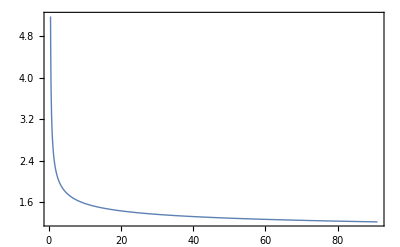

```mathematica
Plot[{√(4π αs1L[k])},{k,0.5,91},PlotRange->All,PlotStyle->Thick,Frame->True]
```

```mathematica
αs1L[91]
```

0.118